```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.1/11.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.1/~$11.1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/6 семестр/11.1/11.1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

## Dataset 1, 2

```mathematica
dataset1 =raw⟦3⟧⟦2;;⟧⟦All,1;;2⟧
```

{{303.122,12.0809},{303.122,12.0893},{303.366,12.1019},{303.854,12.1188},{304.341,12.1611},{305.317,12.264},{308.244,12.6518},{310.195,13.0454},{312.878,13.6813},{316.293,14.6425},{317.756,15.1657},{321.659,16.863},{325.073,18.8646},{328.244,20.5948},{330.927,22.7485},{335.073,26.1693},{339.463,30.5309},{343.122,34.4606},{346.293,38.2475},{351.171,45.2016},{354.098,49.7217},{356.537,53.5465},{365.073,70.1718},{369.22,79.1027},{371.171,84.8907},{373.366,89.4735},{376.537,99.4434},{379.707,108.091},{382.146,115.249},{385.073,124.304},{388.244,135.429},{390.439,144.42},{392.634,152.654}}

```mathematica
dataset2 =raw⟦4⟧⟦2;;⟧⟦All,1;;2⟧
```

{{303.122,19.1976},{303.122,19.187},{303.366,19.187},{303.854,19.1764},{304.341,19.1659},{305.317,19.1342},{308.244,18.9881},{310.195,18.8748},{312.878,18.7024},{316.293,18.4937},{317.756,18.4154},{321.659,18.1656},{325.073,17.9593},{328.244,17.7759},{330.927,17.5784},{335.073,17.3505},{339.463,17.0949},{343.122,16.8957},{346.293,16.7172},{351.171,16.4641},{354.098,16.3098},{356.537,16.1885},{365.073,15.7775},{369.22,15.5867},{371.171,15.5034},{373.366,15.4005},{376.537,15.2654},{379.707,15.113},{382.146,15.0152},{385.073,14.8995},{388.244,14.7918},{390.439,14.6795},{392.634,14.5934}}

```mathematica
line2 = LinearModelFit[dataset2,{1,T},T]
```

FittedModel[35.2419-0.0530678 T]

```mathematica
datasetbonus = raw⟦6⟧⟦2;;⟧⟦All,1;;2⟧
```

{{303.122,181.3},{303.122,181.4},{303.366,181.4},{303.854,181.5},{304.341,181.6},{305.317,181.9},{308.244,183.3},{310.195,184.4},{312.878,186.1},{316.293,188.2},{317.756,189.},{321.659,191.6},{325.073,193.8},{328.244,195.8},{330.927,198.},{335.073,200.6},{339.463,203.6},{343.122,206.},{346.293,208.2},{351.171,211.4},{354.098,213.4},{356.537,215.},{365.073,220.6},{369.22,223.3},{371.171,224.5},{373.366,226.},{376.537,228.},{379.707,230.3},{382.146,231.8},{385.073,233.6},{388.244,235.3},{390.439,237.1},{392.634,238.5}}

```mathematica
line3 = LinearModelFit[datasetbonus,{1,T},T]
```

FittedModel[-16.3334+0.648633 T]

```mathematica
line3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -16.3334 | 0.998198 | -16.3629 | 8.39454×10^-17
T | 0.648633 | 0.00290517 | 223.268 | 2.82594×10^-51

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 35.2419 | 0.192963 | 182.636 | 1.4244×10^-48
T | -0.0530678 | 0.000561602 | -94.4936 | 1.02039×10^-39

```mathematica
exp = NonlinearModelFit[dataset1⟦12;;⟧,A Exp[B/T],{A,B},T]
```

FittedModel[4.34821×10^6 ⅇ^(-4027.38/T)]

```mathematica
exp["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 18354.7 | 772.762 | 23.7521 | 2.57845×10^-13
U0 | 5.83894 | 0.0845427 | 69.065 | 3.3795×10^-20
σ | 1.75136 | 0.0863202 | 20.2891 | 2.56263×10^-12

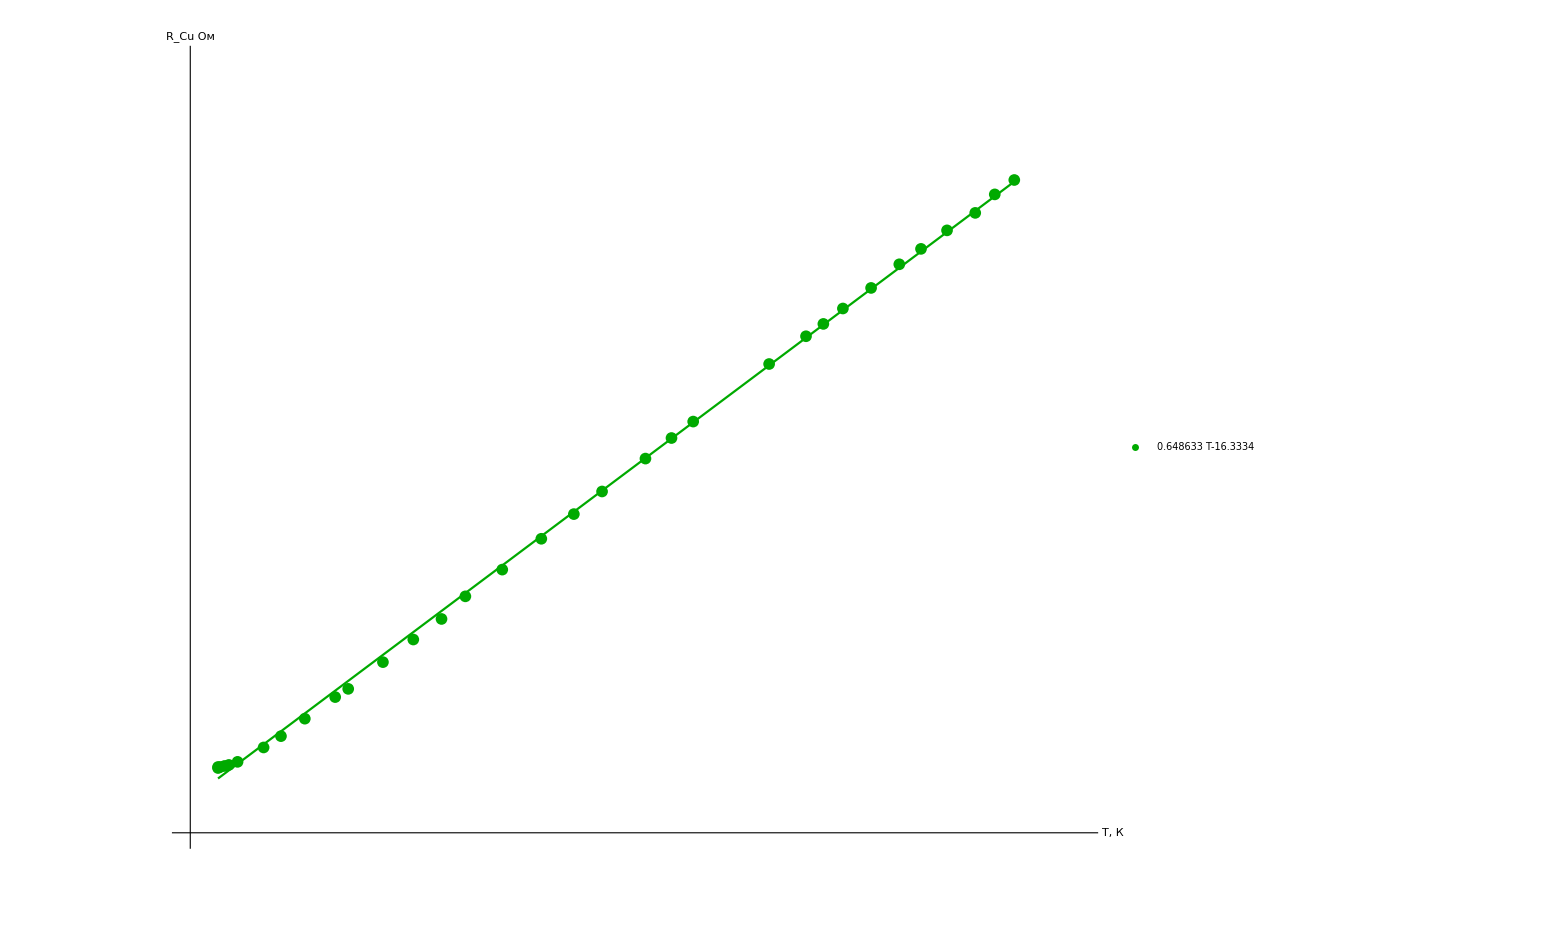

```mathematica
Show[
ListPlot[
{datasetbonus},
PlotRange-> {{300,400},{175,250}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 10]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["T, К", Large], Style["R_(:0421u) Ом", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 2.5],Range[-1000,1000, 2.5]},
LabelStyle->Black,
PlotStyle->Darker@Green,
(*Joined->True,
InterpolationOrder->3,*)
PlotLegends->Placed[LineLegend[
{Normal@line3},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[{line3[x]},{x,303.122,392.634}(*,*)
(*PlotLegends->Placed[LineLegend[
{Normal@exp, Normal@line2},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.5]}
]*),
PlotStyle->Darker@Green
]
]
```

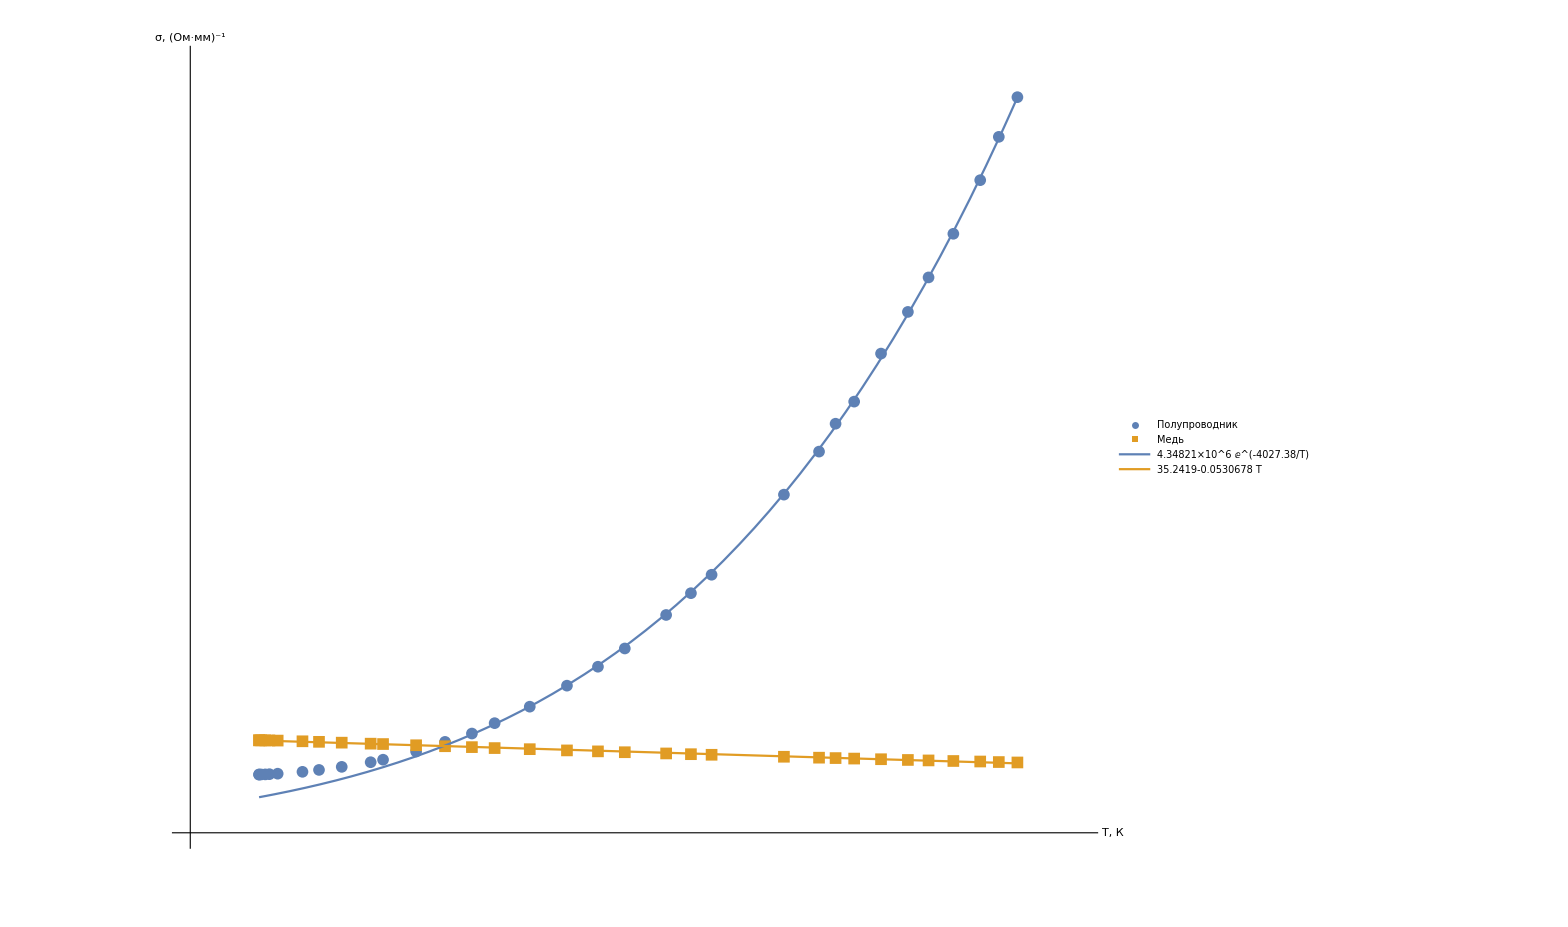

```mathematica
Show[
ListPlot[
{dataset1, dataset2},
PlotRange-> {{295,400},{0,160}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 10]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["T, К", Large], Style["σ, (Ом·мм)^-1", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 2.5],Range[-1000,1000, 5]},
LabelStyle->Black,
(*Joined->True,
InterpolationOrder->3,*)
PlotLegends->Placed[LineLegend[
{"Полупроводник", "Медь"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[{exp[x],line2[x]},{x,303.122,392.634},
PlotLegends->Placed[LineLegend[
{Normal@exp, Normal@line2},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.5]}
]
]
]
```

```mathematica
dataset3 =raw⟦5⟧⟦2;;⟧⟦All,1;;2⟧
```

{{3.299,2.49163},{3.299,2.49232},{3.29635,2.49337},{3.29106,2.49476},{3.28578,2.49825},{3.27528,2.50667},{3.24418,2.5378},{3.22378,2.56844},{3.19613,2.61603},{3.16163,2.68393},{3.14707,2.71903},{3.10889,2.82512},{3.07623,2.93729},{3.04652,3.02504},{3.02182,3.1245},{2.98442,3.26459},{2.94583,3.41874},{2.91442,3.53982},{2.88773,3.64408},{2.84762,3.81113},{2.82408,3.90644},{2.80476,3.98055},{2.73918,4.25095},{2.70842,4.37075},{2.69418,4.44136},{2.67834,4.49394},{2.65578,4.59959},{2.63361,4.68297},{2.6168,4.74709},{2.59691,4.82273},{2.5757,4.90845},{2.56122,4.97272},{2.5469,5.02818}}

```mathematica
line1 = LinearModelFit[dataset3⟦12;;⟧,{1,T},T]
```

FittedModel[15.1632-3.98237 T]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 15.1632 | 0.0501092 | 302.602 | 4.34467×10^-38
T | -3.98237 | 0.0178981 | -222.502 | 2.03218×10^-35

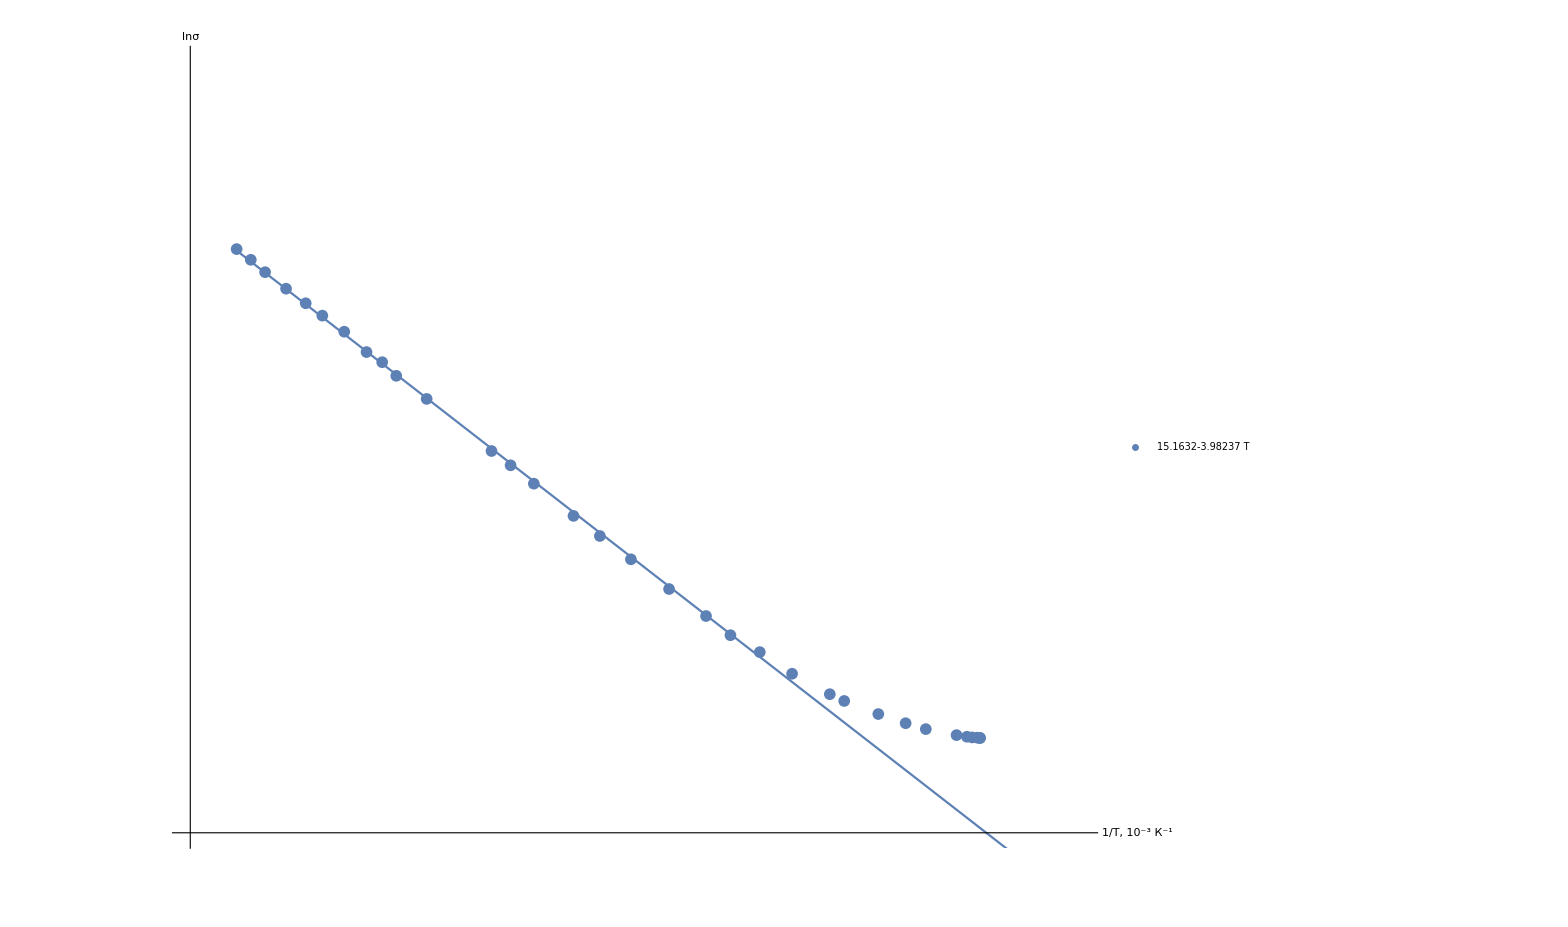

```mathematica
Show[
ListPlot[
{ dataset3},
PlotRange-> {{2.50,3.4},{2,6}},
Ticks-> {Range[-1000,1000, 0.1],Range[-1000,1000, 0.5]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["1/T, 10^-3 (:041a)^-1", Large], Style["lnσ", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.025],Range[-1000,1000, 0.125]},
LabelStyle->Black,
(*Joined->True,
InterpolationOrder->3,*)
PlotLegends->Placed[LineLegend[
{Normal[line1]},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.5],Scaled[0.75]}
]
],
Plot[line1[x],{x,2.5469,3.5955}]
]
```